```mathematica
FP[n_,α_,β_]:=Module[
{
Δ0,Δ1,,f1,f2,γ,κ
,root,AllRoots,case,outcome
},
γ=1.0;
κ=0.1;
Δ0=(-1+(1+ⅇ^α)/(1+ⅇ^(α-β/n))) γ-κ;
Δ1=(1+ⅇ^α) (1/(1+ⅇ^(α-β))-1/(1+ⅇ^(α+(-1+1/n) β))) γ-κ;
f1[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (1+p(n-1))/n-α)])-κ;
f2[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (p(n-1))/n-α)]);

(*root[x0_]:=Module[{r},
r=FindRoot[
p(1-p)(f1[p]-f2[p])==0,{p,0.5}
];
If[r⟦1,2⟧<0,0,If[r⟦1,2⟧>1.0,1.0,r⟦1,2⟧]]
];
AllRoots=Round[root[#],0.0001]&/@Range[0.05,0.95,0.05];
DeleteDuplicates[AllRoots]*)
Which[
(Δ0>0&&Δ1>0),outcome={"Dominance of P",1},
(Δ0>0&&Δ1<0),outcome={"Coexistence",2},
(Δ0<0&&Δ1<0),outcome={"Dominance of N",3},
(Δ0<0&&Δ1>0),outcome={"Bi-Stabillity",4}
];
{Δ0,Δ1,outcome}

](*END of MODULE*)
```

### Case 1: Dominance of Producers

```mathematica
FP[10,2,2]
```

{0.0899965,0.31806,{Dominance of P,1}}

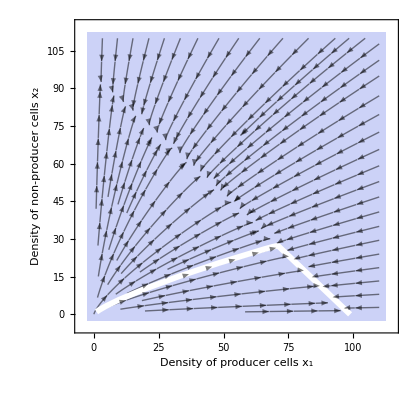

```mathematica
α=2.0;
β=2.0;
κ=0.1;
γ=1.0;
n=5.;
CC=100;
δ=0.05;


f1[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (1+p(n-1))/n-α)])-κ;
f2[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (p(n-1))/n-α)]);

sp=StreamDensityPlot[
{
f1[x/(x+y)]x(1-(x+y)/CC)-x δ
,
f2[x/(x+y)]y(1-(x+y)/CC)-y δ
}
,{x,0.001,110},{y,0.001,110}
,PlotRange->{{-5,115},{-5,115}}
,StreamPoints->Automatic
,AxesLabel-> "s"
,StreamStyle->Opacity[0.5,Black]
,Frame->True
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Density of producer cells x_1","Density of non-producer cells x_2"}
,ColorFunction->Opacity[0.1,ColorData["DeepSeaColors"]]
];
sol=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(n-1))/n-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(n-1))/n-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
, x[0]==1,y[0]==1
},{x,y},{t,1000}];


pp1=ParametricPlot[{x[t],y[t]}/.sol,{t,0,1000},PlotRange->{All,All},AspectRatio->1,PlotStyle->{Thickness[0.01],ColorData["CherryTones"][1.0]}]/.Line->Arrow;

Show[sp,pp1]
```

### Case 2: Coexistence

```mathematica
FP[10,0.5,2]
```

{0.0271832,-0.0159309,{Coexistence,2}}

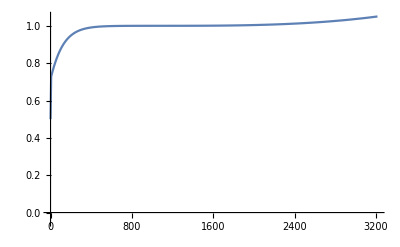

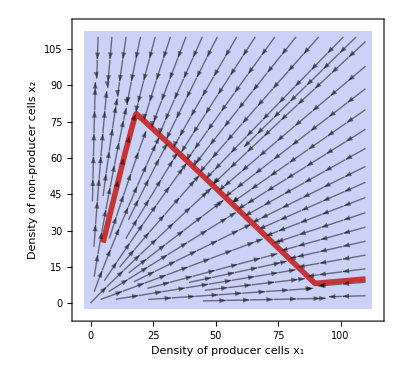

```mathematica
α=0.5;
β=4.0;
κ=0.1;
γ=1.0;
n=10.;
CC=100;
δ=0.05;


f1[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (1+p(n-1))/n-α)])-κ;
f2[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (p(n-1))/n-α)]);

sol1=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(n-1))/n-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(n-1))/n-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
, x[0]==5,y[0]==25
},{x,y},{t,0,10^6}];
sol2=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(n-1))/n-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(n-1))/n-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
, x[0]==110,y[0]==10
},{x,y},{t,0,10^6}];

Plot[
{x[t]/(x[t]+y[t])}/.sol,{t,0,20000}
,PlotRange->{All,{-0.05,1.05}}
]
sp=StreamDensityPlot[
{
f1[x/(x+y)]x(1-(x+y)/CC)-x δ
,
f2[x/(x+y)]y(1-(x+y)/CC)-y δ
}
,{x,0.001,110},{y,0.001,110}
,PlotRange->{{-5,115},{-5,115}}
,StreamPoints->Automatic
,AxesLabel-> "s"
,StreamStyle->Opacity[0.5,Black]
,Frame->True
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,AspectRatio->0.95
,FrameLabel->{"Density of producer cells x_1","Density of non-producer cells x_2"}
,ColorFunction->Opacity[0.1,ColorData["DeepSeaColors"]]
];
pp1=ParametricPlot[{x[t],y[t]}/.sol1,{t,0,5000},PlotRange->{All,All},AspectRatio->1,PlotStyle->{Thickness[0.01],ColorData["CherryTones"][1/3]}]/.Line->Arrow;
pp2=ParametricPlot[{x[t],y[t]}/.sol2,{t,0,8000},PlotRange->{All,All},AspectRatio->1,PlotStyle->{Thickness[0.01],ColorData["CherryTones"][1/3]}]/.Line->Arrow;


Show[sp,pp1,pp2]
```

### Case 3: Dominance of Non-Producer Cells

```mathematica
FP[10,0.5,2]
```

{0.0271832,-0.0159309,{Coexistence,2}}

-Graphics-

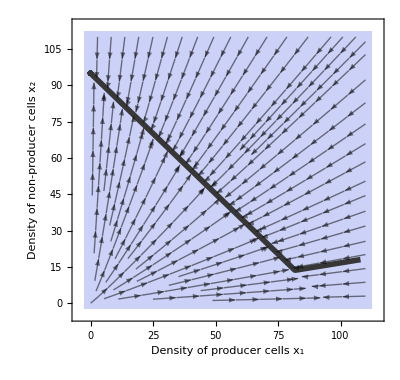

```mathematica
α=1.0;
β=0.25;
κ=0.1;
γ=1.0;
n=5.;
CC=100;
δ=0.05;


f1[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (1+p(n-1))/n-α)])-κ;
f2[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (p(n-1))/n-α)]);

sol1=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(n-1))/n-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(n-1))/n-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
, x[0]==108,y[0]==18
},{x,y},{t,0,10^6}];

Plot[
{x[t]/(x[t]+y[t])}/.sol,{t,0,20000}
,PlotRange->{All,{-0.05,1.05}}
]
sp=StreamDensityPlot[
{
f1[x/(x+y)]x(1-(x+y)/CC)-x δ
,
f2[x/(x+y)]y(1-(x+y)/CC)-y δ
}
,{x,0.001,110},{y,0.001,110}
,PlotRange->{{-5,115},{-5,115}}
,StreamPoints->Automatic
,AxesLabel-> "s"
,StreamStyle->Opacity[0.5,Black]
,Frame->True
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,AspectRatio->0.95
,FrameLabel->{"Density of producer cells x_1","Density of non-producer cells x_2"}
,ColorFunction->Opacity[0.1,ColorData["DeepSeaColors"]]
];
pp1=ParametricPlot[{x[t],y[t]}/.sol1,{t,0,15000},PlotRange->{All,All},AspectRatio->1,PlotStyle->{Thickness[0.01],ColorData["CherryTones"][0.0]}]/.Line->Arrow;


Show[sp,pp1]
```

### Case 4: Bi-Stability

```mathematica
FP[10,1.5,1]
```

{-0.0156336,0.0271586,{Bi-Stabillity,4}}

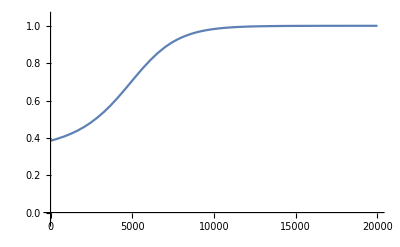

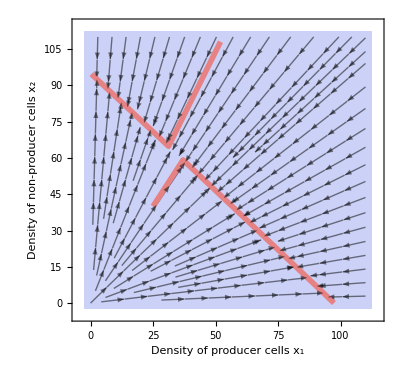

```mathematica
α=1.5;
β=1.0;
κ=0.1;
γ=1.0;
n=10.;
CC=100;
δ=0.05;


f1[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (1+p(n-1))/n-α)])-κ;
f2[p_]:=γ(1+ⅇ^α)/(1+Exp[-(β (p(n-1))/n-α)]);

sol1=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(n-1))/n-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(n-1))/n-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
, x[0]==25,y[0]==40
},{x,y},{t,0,10^6}];
sol2=NDSolve[
{
x'[t]==(γ(1+ⅇ^α)/(1+Exp[-(β (1+x[t]/(x[t]+y[t])(n-1))/n-α)])-κ) x[t](1-(x[t]+y[t])/CC)-x [t]δ
,
y'[t]==γ(1+ⅇ^α)/(1+Exp[-(β (x[t]/(x[t]+y[t])(n-1))/n-α)])y[t](1-(x[t]+y[t])/CC)-y [t]δ
, x[0]==52,y[0]==108
},{x,y},{t,0,10^6}];

Plot[
{x[t]/(x[t]+y[t])}/.sol1,{t,0,20000}
,PlotRange->{All,{-0.05,1.05}}
]
sp=StreamDensityPlot[
{
f1[x/(x+y)]x(1-(x+y)/CC)-x δ
,
f2[x/(x+y)]y(1-(x+y)/CC)-y δ
}
,{x,0.001,110},{y,0.001,110}
,PlotRange->{{-5,115},{-5,115}}
,StreamPoints->Automatic
,AxesLabel-> "s"
,StreamStyle->Opacity[0.5,Black]
,Frame->True
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,AspectRatio->0.95
,FrameLabel->{"Density of producer cells x_1","Density of non-producer cells x_2"}
,ColorFunction->Opacity[0.1,ColorData["DeepSeaColors"]]
];
pp1=ParametricPlot[{x[t],y[t]}/.sol1,{t,0,15000},PlotRange->{All,All},AspectRatio->1,PlotStyle->{Thickness[0.01],ColorData["CherryTones"][2/3]}]/.Line->Arrow;


pp2=ParametricPlot[{x[t],y[t]}/.sol2,{t,0,15000},PlotRange->{All,All},AspectRatio->1,PlotStyle->{Thickness[0.01],ColorData["CherryTones"][2/3]}]/.Line->Arrow;


Show[sp,pp1,pp2]
```